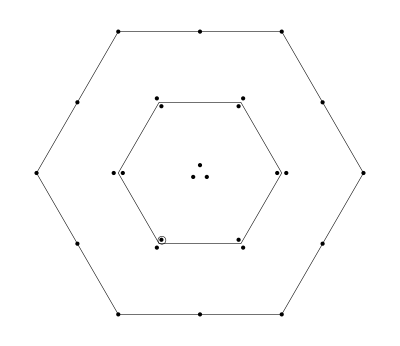

Y=-1.5,  I_3=-0.5

2(sd+ds)(ūd̄+d̄ū)-ss(ūs̄+s̄ū)-(us+su)ūū

```mathematica
(*-------------------------------*)
```

The current J:

2 (d_a^T C1 s_b+s_a^T C1 d_b) ((d̄)_a 1C((ū)_b)^T)+2 (d_a^T C1 s_b+s_a^T C1 d_b) ((d̄)_b 1C((ū)_a)^T)+2 (d_a^T C1 s_b+s_a^T C1 d_b) ((ū)_a 1C((d̄)_b)^T)+2 (d_a^T C1 s_b+s_a^T C1 d_b) ((ū)_b 1C((d̄)_a)^T)-(s_a^T C1 s_b) ((s̄)_a 1C((ū)_b)^T+(s̄)_b 1C((ū)_a)^T)-((ū)_a 1C((ū)_b)^T) (s_a^T C1 u_b+u_a^T C1 s_b)-(s_a^T C1 s_b) ((ū)_a 1C((s̄)_b)^T+(ū)_b 1C((s̄)_a)^T)-((ū)_b 1C((ū)_a)^T) (s_a^T C1 u_b+u_a^T C1 s_b)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
2 (d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 s)+2 (d̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 d)+2 (d̄ γ^μ d ū γ^μ s)+2 (d̄ γ^μ s ū γ^μ d)+(s̄(γ̄)^5 s-2 (d̄(γ̄)^5 d)) (ū(γ̄)^5 s)-2 (d̄(γ̄)^5 s ū(γ̄)^5 d)+d̄ σ^μν d ū σ^μν s+d̄ σ^μν s ū σ^μν d+(s̄ 1s-2 (d̄ 1d)) (ū 1s)-2 (d̄ 1s ū 1d)-s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 s-s̄ γ^μ s ū γ^μ s-ū(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u-ū γ^μ s ū γ^μ u+ū(γ̄)^5 s ū(γ̄)^5 u-1/2 (s̄ σ^μν s ū σ^μν s)-1/2 (ū σ^μν s ū σ^μν u)+ū 1s ū 1u
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(384 π^6)+(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(96 π^5)-(2 ⟨ d̄ d⟩ log(-q^2/μ^2) (m_d+m_s+m_u) q^4)/(3 π^4)-(⟨ s̄ s⟩ log(-q^2/μ^2) (4 m_d+4 m_s+m_u) q^4)/(6 π^4)-(⟨ ū u⟩ log(-q^2/μ^2) (4 m_d+m_s+4 m_u) q^4)/(6 π^4)-(8 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(25 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(864 π^6)+(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2+(8 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(23 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(18 π^2)-(95 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(36 π^2)-(95 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(36 π^2)-(95 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(36 π^2)-(13 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(72 π^2)-(13 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(72 π^2)-(95 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(36 π^2)-(13 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(72 π^2)-(13 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(72 π^2)-(8 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(9 π q^2)-(5 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(18 π q^2)-(5 ⟨ GG ⟩ ⟨ ū u⟩^2)/(18 π q^2)-⟨ d̄ Gd⟩^2/(24 π^2 q^2)+(127 ⟨ s̄ Gs⟩^2)/(1152 π^2 q^2)+(127 ⟨ ū Gu⟩^2)/(1152 π^2 q^2)+(4 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)+(4 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)-(5 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)+(145 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(144 π^2 q^2)+(145 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(144 π^2 q^2)+(127 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(576 π^2 q^2)-(2 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (16 m_s-16 m_u))/(9 q^2)-(8 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (-8 m_d+4 m_s-8 m_u))/(9 q^2)+(32 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (2 m_s+m_u))/(9 q^2)+(32 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (m_s+2 m_u))/(9 q^2)-(8 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (-8 m_d-8 m_s+4 m_u))/(9 q^2)-(2 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (16 m_u-16 m_s))/(9 q^2)+(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (32 m_d+20 (m_s+m_u)))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

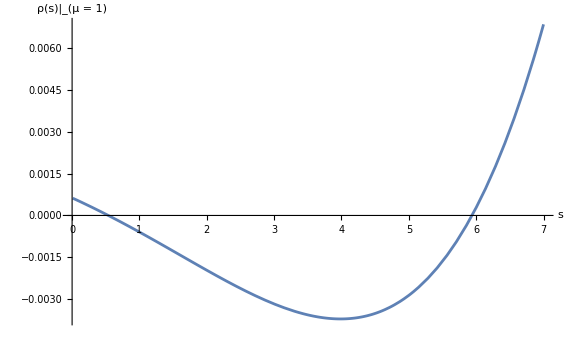
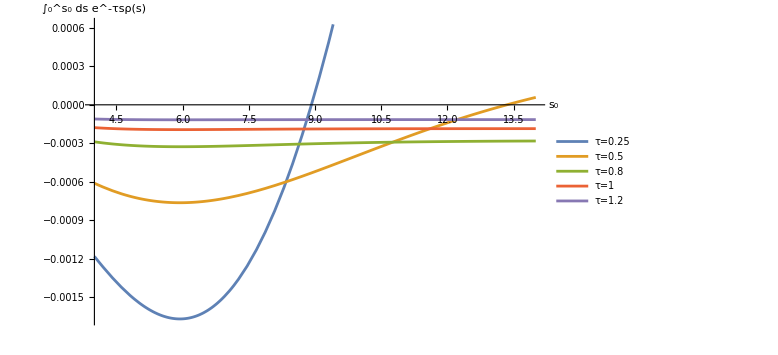

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

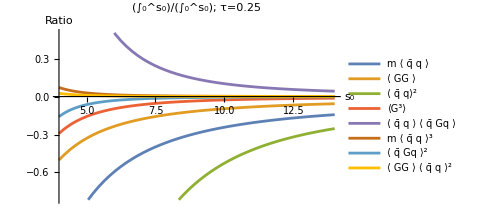
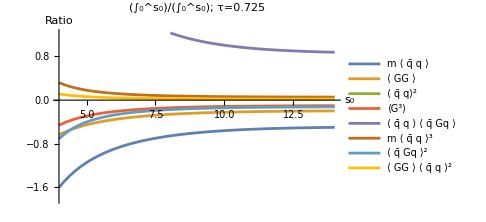
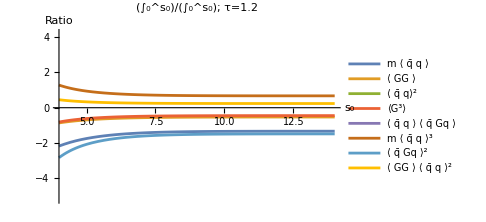

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

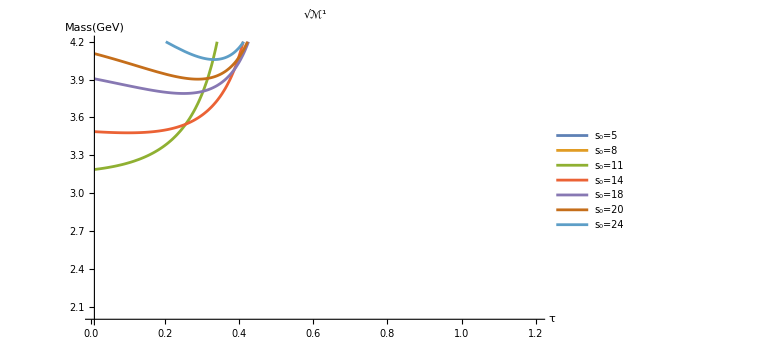
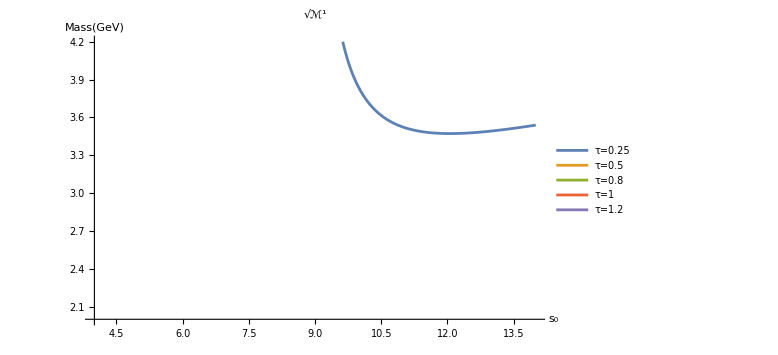

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

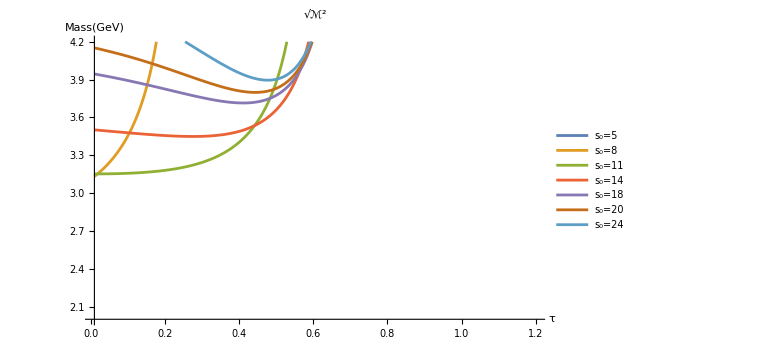
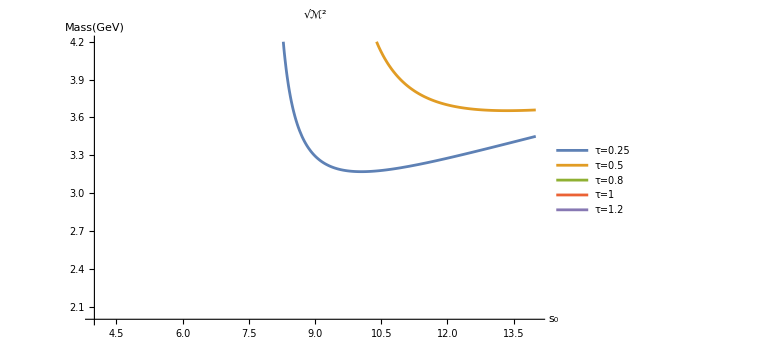

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

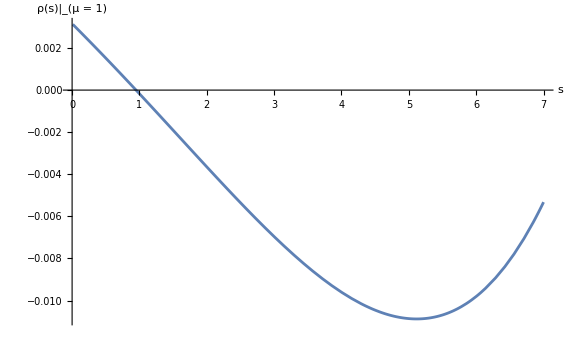
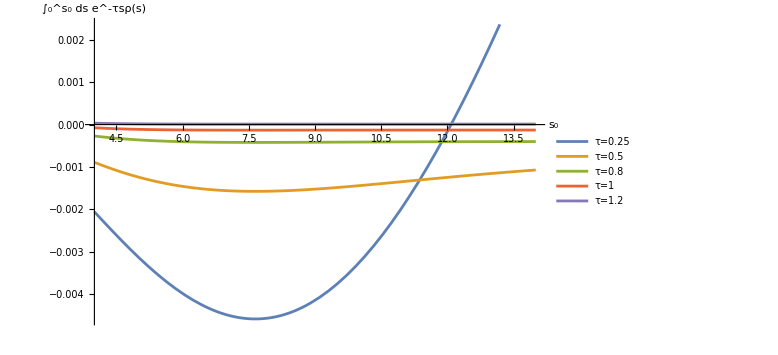

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

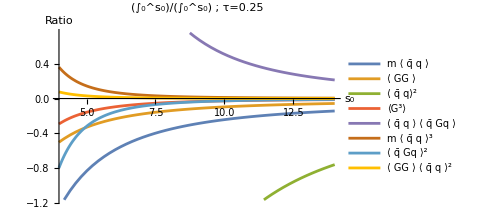
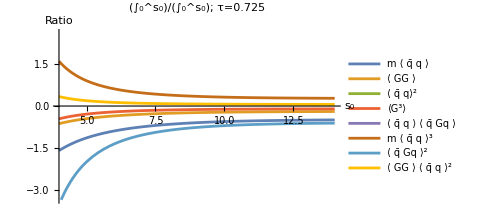
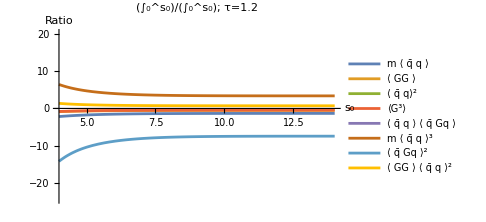

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

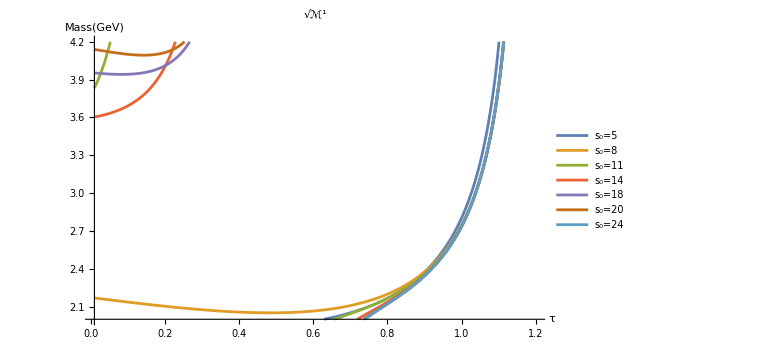
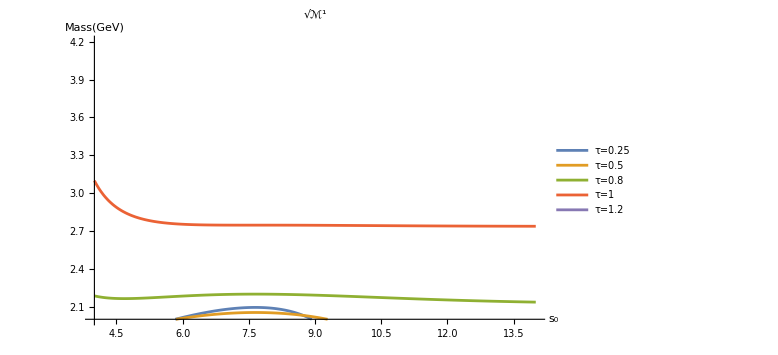

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5